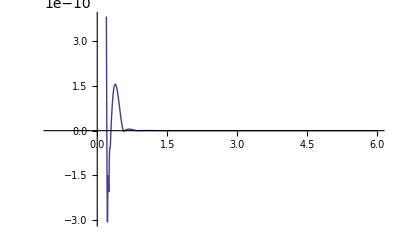

```mathematica
f[t_,x_[t_],x_'[t_],ϵ_]=ϵ*x'[t]-x[t]*(Exp[x[t]]-2);
sol=NDSolve[{f[t,x[t],x'[t],0.01]==0,x[t/;t≤0]==0.1},x,{t,-1,6}];
Plot[{x[t]}/.sol,{t,-1,6}]
```